```mathematica
Reabs[base_,effect_] :=base^(1/effect);
```

```mathematica
Reabs [0.6,20]
```

0.974782

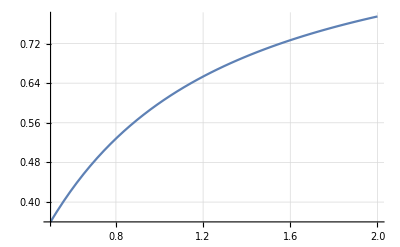

```mathematica
Plot[Reabs[0.9,x],{x,0.5,2}, GridLines ->Automatic]
```

```mathematica
Glomerulus
Real IO vstupuoy jsou  otherCations a ProteinAnions
-Graphics-
část kationtů se váže na proteiny, proto do glomerulárního filtrátu teče o toto tuto koncentraci méně kationtů (v daném případě: sodíku a draslíku)

Physiolibrary.Chemical.Interfaces.ChemicalPort_b q_out ;
Physiolibrary.Chemical.Interfaces.ChemicalPort_a q_in ;
Physiolibrary.Types.RealIO.VolumeDensityOfChargeInput otherCations;
Physiolibrary.Types.RealIO.VolumeDensityOfChargeInput ProteinAnions;
Physiolibrary.Types.Fraction KAdjustment;
Physiolibrary.Types.VolumeDensityOfCharge Cations;
```

```mathematica
equation
q_in.q+q_out.q=0;
Cations=q_in.conc*Modelica.Constants.F+otherCations;
Anions=Cations;
KAdjustment=(Cations-(Anions-ProteinAnions))/(Cations+(Anions-ProteinAnions));
q_out.conc=(1-KAdjustment)*q_in.conc;
```